### Time weighted martingale: Traj and quad variation. N = 256, k =3. Run for N * N steps, record values every N steps. Data:

```mathematica
M = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.000115893,0,0,0,0,0,0,0,0,0,-0.000284289,-0.000220722,-0.000192139,-0.000199055,0,0,0,0.000157897,0,0.000516463,0,-0.000206478,-0.000481344,-0.000677566,-0.000331199,-0.000475531,0,0.000194077,0.000828512,0.000390087,0.000125395,0.000405015,0.000867003,0.000854891,0.00146657,0.00062055,0.000176283,0.000977214,0.000204711,0.000286902,0.000442994,-0.000773291,-0.00172929,-0.00126293,-0.00182848,-0.00265325,-0.006809,-0.00321129,-0.00223631,-0.000942156,-0.00245124,-0.0029034,-0.00204186,-0.00405157,-0.00339675,0.00106181,0.0063399,0.00932055,0.00388567,0.00402058,-0.00239094,-0.000658424,0.00266377,0.00190099,-0.00122461,0.00335591,0,0.00273124,-0.00169463,-0.00277225,0.0020066,0.00969962,-0.00126644,0.0280469,0.012496,-0.00424485,0.000649148,-0.0109552,-0.0052348,-0.0299726,-0.0193571,0.0214311,0.00821924,-0.00785376,0.0209758,-0.0205445,-0.0123212,-0.0234051,-0.0447927,-0.0317119,0.00832737,-0.0140115,0.0428617,0.0305763,-0.0930656,-0.0224975};
MQ = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000106742,0.00012475,0.000144422,0.000164837,0.000190486,0.000219992,0.000258232,0.000298723,0.000336779,0.000398124,0.000458824,0.000535575,0.000618896,0.000721484,0.000836603,0.000996909,0.00114696,0.00132255,0.00154109,0.00179929,0.0021194,0.00243414,0.00278342,0.00316806,0.00361506,0.00413957,0.00477319,0.00547178,0.00643125,0.00754535,0.00874196,0.0103699,0.011933,0.0140053,0.0161202,0.0187591,0.0216843,0.0249436};
Dphi = {-0.0694001,0.0378097,0.0235217,0.0949993,0.0109305,0.0236321,0.070351,0.0438424,0.11621,0.0584607,-0.101551,-0.0160129,-0.063888,-0.136134,-0.0981964,-0.0120312,-0.0682532,-0.190276,-0.214965,-0.122149,-0.0451328,-0.0233214,0.0471806,0.0498274,-0.0413581,-0.0650651,-0.0616713,-0.0785786,-0.0261992,-0.000437935,0.0156934,0.0168513,0.0932553,-0.0339979,-0.07732,-0.0728256,-0.00623179,0.0280108,0.103142,0.0694391,0.156998,0.168502,0.12779,0.103506,0.0454715,-0.0404874,0.00566835,0.0602095,0.0253405,-0.0355366,-0.100356,-0.171406,-0.226761,-0.199031,-0.15591,-0.200069,-0.136128,-0.00731943,-0.0452126,0.0278647,0.124065,-0.0151142,0.0490206,0.0937952,0.108408,0.0909629,-0.00461882,0.00474649,-0.0242802,0.0117486,0.0548727,0.087872,0.111156,0.0607136,0.0827918,0.0113685,0.0842095,0.00888061,0.0484617,-0.034585,-0.051925,-0.0730007,-0.057761,-0.00906211,0.157811,0.156543,0.168736,0.275018,0.298127,0.234339,0.213183,0.144509,0.143257,0.112186,0.17789,0.0897329,0.151894,0.1205,0.0502247,0.0460721,-0.0551182,-0.0979999,-0.105997,-0.0216612,0.0661464,0.105014,0.117311,0.168833,0.160593,0.161873,0.206663,0.236669,0.189325,0.146446,0.000973868,0.0285292,0.00958001,0.0813609,0.0839332,0.0683373,0.09198,-0.0211069,0.0627828,0.0546784,-0.0648795,0.0124358,-0.0131937,-0.0652418,0.00438971,0.061332,-0.0438581,0.0487947,0.00413669,-0.054508,-0.0206459,0.0789669,0.0751945,0.165847,0.233224,0.186793,0.226339,0.219616,0.228614,0.162674,0.116321,0.0893691,0.0804541,0.134333,0.1027,0.111739,0.071476,0.0678406,-0.0017955,-0.022189,-0.00649533,0.111727,-0.00030426,0.0214715,0.0260254,0,-0.0718668,-0.00316338,0.100512,0.0564092,0.0145913,0.0804674,0.0421301,0.0678168,0.0436236,0.00370668,-0.110256,-0.0747178,-0.0641738,-0.0704702,0.0359497,0.0188879,0.0352561,0.066986,0.0126917,0.160724,0.00943898,-0.0269536,-0.0927233,-0.132272,-0.0566182,-0.0865243,-0.00633196,0.0254997,0.122911,0.0639269,0.0283563,0.0598912,0.109485,0.111742,0.169536,0.0955175,0.0589262,0.113786,0.0603434,0.0665584,0.0749509,0.0104394,-0.0413858,-0.0213057,-0.0494789,-0.0813915,-0.244928,-0.106004,-0.0728227,-0.0310105,-0.0703544,-0.0774068,-0.053864,-0.107024,-0.0889661,0.00664822,0.102779,0.157322,0.06631,0.0706583,-0.0214205,-0.00221449,0.0342231,0.023725,-0.0133026,0.0343876,0.00590145,0.036434,-0.00425476,-0.0146503,0.0116448,0.0659406,-0.00305909,0.157623,0.0799176,0.0122046,0.0370099,-0.0180619,0.00965196,-0.0731197,-0.0406938,0.0800811,0.0411919,0.00405439,0.0765634,-0.0207238,-0.00828858,-0.0217361,-0.0602989,-0.0313665,0.028788,-0.00688696,0.0738542,0.0672487,-0.0887962,-0.015296};
DphiQ = {0.00358126,0.00736492,0.0109215,0.0154802,0.0198812,0.0239394,0.0280641,0.0318371,0.0357698,0.0394437,0.0433457,0.0472026,0.0509131,0.0546903,0.058407,0.0620844,0.06562,0.0691757,0.0728557,0.0764839,0.0798776,0.0835207,0.0878881,0.0918872,0.095841,0.0997827,0.103714,0.107019,0.110685,0.114495,0.118336,0.1226,0.126112,0.129838,0.133613,0.137414,0.141282,0.14551,0.149279,0.153162,0.156974,0.160632,0.164726,0.168565,0.17232,0.1763,0.180589,0.184476,0.188338,0.1924,0.196557,0.2001,0.204278,0.207834,0.211704,0.215411,0.219067,0.223193,0.226703,0.230827,0.235385,0.239314,0.243257,0.247302,0.251056,0.254898,0.258781,0.262716,0.266672,0.270332,0.274182,0.278144,0.282054,0.285547,0.289375,0.293743,0.298024,0.302204,0.305938,0.30976,0.313488,0.317423,0.321363,0.325359,0.329265,0.333716,0.337818,0.341391,0.345384,0.349659,0.353312,0.35686,0.360738,0.364748,0.368444,0.372063,0.376229,0.380118,0.383822,0.38791,0.391777,0.395235,0.398947,0.402452,0.406649,0.410259,0.414048,0.418078,0.421924,0.42578,0.42946,0.432847,0.436851,0.440921,0.444568,0.44877,0.452971,0.456998,0.460613,0.464096,0.467845,0.471856,0.475836,0.479829,0.484391,0.488508,0.492476,0.496449,0.500462,0.504355,0.508178,0.512011,0.516327,0.52066,0.524476,0.528174,0.532298,0.535972,0.540163,0.544045,0.548106,0.551475,0.555474,0.559187,0.563139,0.567644,0.571286,0.574912,0.578721,0.582463,0.586146,0.589836,0.593821,0.597805,0.601857,0.605697,0.609524,0.613218,0.617495,0.621144,0.625054,0.629099,0.633164,0.637363,0.641441,0.64526,0.649193,0.652898,0.656588,0.660351,0.664482,0.668945,0.672931,0.676683,0.680458,0.684308,0.688472,0.691873,0.695114,0.699047,0.703028,0.706406,0.710152,0.713808,0.717929,0.721852,0.725123,0.729087,0.732999,0.736259,0.74003,0.744447,0.748441,0.752256,0.756042,0.760022,0.763907,0.768309,0.77195,0.775476,0.779228,0.783272,0.786815,0.790423,0.794119,0.798357,0.802419,0.806232,0.810281,0.81399,0.817649,0.821666,0.825776,0.829358,0.833172,0.837432,0.840857,0.844994,0.848856,0.85298,0.856946,0.860457,0.864255,0.868039,0.872256,0.876098,0.87926,0.883734,0.887512,0.891563,0.895369,0.899338,0.903206,0.907968,0.911831,0.915624,0.919711,0.923742,0.928136,0.931935,0.935574,0.93912,0.942572,0.94616,0.949838,0.953403,0.957597,0.96178,0.965657,0.970117,0.973789,0.97804,0.981831,0.985919,0.989824,0.993609};
```

### Analysis

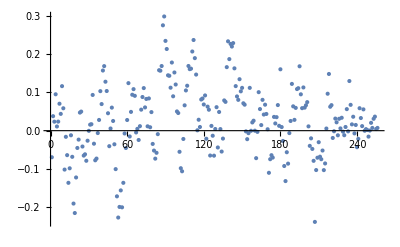

```mathematica
ListPlot[Dphi - M]
```

```mathematica
Dphi[[256]]- M[[256]]
1/256.
```

0.0072015

0.00390625

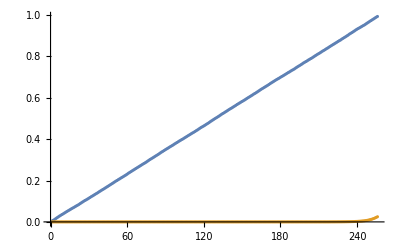

```mathematica
ListPlot[{DphiQ, MQ}]
```

### Time weighted martingale: Traj and quad variation. N = 512, k =3. Run for N * N steps, record values every N steps. Data:

```mathematica
M2 = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000103465,0.000109522,0.00011818,0.000117544,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.000137501,0,0,0,0.000161132,0.000137706,0,0.000113651,0,0,0,-0.000155447,-0.000114567,0,0,0.000144419,0,-0.000271436,-0.000374026,-0.000209861,-0.000256778,-0.000190281,0,0,0,0.000103729,0.000208995,0.00043757,0.000679914,0.00062424,0.000362956,0.000120236,0.000334619,0.000123074,0,-0.000394817,-0.000541619,-0.000360478,-0.000203145,-0.000113321,0,-0.000133349,-0.000676372,-0.000752488,0,0.000226668,0.000123442,0.000393645,0.000651415,0.000720407,0.000253096,0.000837651,0.000753696,0.000780098,-0.000177149,0.000414831,0.000857853,0.00135068,0.00141629,0.00121203,0.00105571,0.00157198,0.00114679,0.000181388,0.00117363,0.00210115,0.00253989,0.00193817,0.00204332,0.000797856,0.00063376,0.000669998,0.00060301,0.000855324,0.0018227,0.00155994,0.00183657,0.00333116,0.00332176,0.00458187,0.00433717,0.00393891,0.00420038,0.00280702,0.00295102,0.00320378,0.00402538,0.00246986,-0.00183956,-0.00482509,-0.00571603,-0.00756903,-0.00517016,-0.00360343,-0.00227034,-0.0011936,-0.00359251,-0.00331099,-0.00237601,0,0.000467179,0.000633273,-0.000947566,-0.000629288,-0.00210855,-0.00189802,-0.00113317,-0.00249408,0.000174988,0,0.000138958,-0.00339186,-0.00503897,-0.000280698,-0.00398964,-0.00215505,-0.000207473,-0.00476515,0.00787392,0.0110113,0.0122947,0.00613708,0.0142219,0.0167073,0.0103176,0.0139015,0.00602482,-0.00580662,-0.0139022,-0.00838063,-0.00818746,-0.011253,-0.00296591,0.00145733,0.00185846,-0.0126985,0.0018114,-0.00875033,-0.00697798,-0.0024997,-0.0154517,-0.00920969,-0.00402231,-0.00368973,-0.00848161,-0.0072012,-0.0110384,-0.0286066,-0.0117367,-0.0147521,-0.00882447,0.0201369,0.0430789,0.0518255,0.0594474,0.0423205,0.0477279,0.0373687,0.0544599,0.0812827,0.0850148,0.0658194,0.0646905,0.0591605,0.0702428,0.0302609,0.0323258,0.0515326,0.0395531,0.0656232,0.0557718,0.0352035,0.0894281,0.0670878,0.00614747,0.0453628,0.0275037,0.0239467,-0.0372605,-0.0362962};
MQ2 = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000102162,0.000110373,0.000119107,0.000128658,0.000138986,0.000149513,0.000160557,0.000172875,0.00018644,0.000201002,0.000215487,0.00023276,0.000250633,0.000269723,0.000290416,0.000314576,0.00033874,0.000363998,0.000390898,0.000422999,0.000455327,0.000489854,0.000524674,0.000568934,0.000610617,0.000657906,0.000704919,0.000758595,0.000818544,0.000882667,0.000947063,0.00102351,0.00110196,0.00118896,0.00127944,0.00138361,0.00148138,0.00159284,0.00171572,0.00186014,0.00198732,0.00213275,0.00229857,0.00247603,0.00266353,0.00285239,0.00305194,0.00327262,0.00350279,0.00377169,0.00406701,0.00438483,0.00471316,0.00507083,0.00547862,0.00589342,0.00637763,0.0068173,0.00739274,0.00793143,0.00853194,0.00917041,0.00982303,0.0106044,0.011463,0.0123604,0.0133956,0.0143262,0.0153828,0.0165172,0.0176792,0.0189322,0.0204823,0.022025,0.0239423,0.0258375};
```

```mathematica
Dphi2 = {0.0482538,-0.0125745,-0.0659909,-0.0349993,-0.0953038,-0.0722686,-0.105579,-0.0603551,-0.0421104,0.0402977,0.0660223,0.0923879,0.156839,0.0203095,-0.0148495,-0.0117393,0.0255054,-0.0597693,-0.0682923,0.0242501,0.0137076,0.0665874,0.124164,0.199358,0.171988,0.222531,0.186192,0.15438,0.119866,0.160197,0.106132,0.148757,0.164486,0.147667,0.108531,0.131712,0.0345432,0.00224541,-0.0164811,0.00898568,0.0369891,0.083395,0.129189,0.146749,0.140346,0.226003,0.190082,0.215451,0.147537,0.195799,0.186397,0.233133,0.19057,0.167761,0.209854,0.203455,0.235737,0.189898,0.16599,0.190613,0.12476,0.104939,0.0930647,0.0786787,0.0996991,0.0744589,0.0305008,0.0474017,-0.0362163,-0.0334305,-0.0194415,-0.039798,-0.0479505,-0.0153488,-0.0324201,-0.0234769,0.0217441,0.00405249,0.0456488,0.0104771,0.0430459,0.109404,0.0611631,0.0449194,0.0693625,0.00920862,0.0978949,0.106097,0.0349716,-0.00548051,0.00141642,0.0290473,0.0527303,0.0648025,0.134148,0.0943615,0.108827,0.124329,0.150438,0.101459,0.153519,0.093531,0.107587,0.054566,0.123948,0.155737,0.103852,0.171517,0.12514,0.0668947,0.0477431,0.0333358,-0.0602074,-0.0674643,-0.03551,-0.0922535,-0.0867935,-0.0480327,0.0650256,0.044859,0.0193626,-0.037449,-0.0687135,-0.0403368,0.0236032,0.045255,0.0332954,0.0490971,0.0762565,0.0940629,0.0928632,0.110142,0.139802,0.0873288,0.068173,0.099792,0.0847813,0.0311101,-0.00585004,-0.00164746,-0.0844937,-0.0540641,0.0274315,0.0175188,-0.00545083,0.0405636,0.0686004,0.0887476,0.0692915,0.0788241,0.0803026,0.0894514,0.0779614,0.0415429,0.0370391,-0.0163525,-0.0229309,0.0326201,0.0459902,0.111518,0.0667142,0.0466452,0.046789,0.0523291,-0.0309655,-0.0403953,-0.0572974,-0.063522,-0.0865909,-0.105083,-0.0970693,-0.0676288,-0.0706873,-0.0937659,-0.120289,-0.120326,-0.103733,-0.122728,-0.0582192,0.000555929,0.0288961,0.0755534,0.0846763,0.115178,0.0510881,0.0611312,0.0830779,0.0886836,0.087851,0.0806984,0.0331722,0.00595648,-0.0117031,-0.0363976,-0.00803406,0.00206979,-0.0495499,-0.105454,-0.0841666,-0.0284223,-0.0926861,-0.104929,-0.116451,-0.103091,-0.0279197,-0.0281226,-0.0245185,-0.0860306,-0.132995,-0.204865,-0.16414,-0.23955,-0.2467,-0.229083,-0.201614,-0.263122,-0.181227,-0.0374306,-0.0445329,-0.00245564,-0.0424593,0.0643467,0.0440425,0.0123113,0.0735093,0.101622,0.217524,0.246732,0.169999,0.12553,0.136736,0.219244,0.254659,0.251716,0.253114,0.243399,0.244667,0.279062,0.30036,0.235498,0.249857,0.177549,0.1809,0.125321,0.101243,0.0664519,0.059561,0.0936371,0.164342,0.0680393,0.0658857,-0.0146075,-0.0234545,-0.0878662,-0.11267,-0.121222,-0.077657,-0.043114,-0.115968,-0.141416,-0.0891252,-0.0940829,-0.0285649,-0.0727299,-0.138432,-0.0638844,-0.0677805,-0.108405,-0.137288,-0.159503,-0.12809,-0.123792,-0.182612,-0.223023,-0.206286,-0.218057,-0.260264,-0.256287,-0.200129,-0.163026,-0.144958,-0.128674,-0.0971905,-0.0949042,-0.111784,-0.155034,-0.163506,-0.0904718,-0.088749,-0.0707288,-0.17887,-0.214737,-0.242352,-0.162356,-0.153869,-0.179399,-0.162251,-0.21748,-0.157457,-0.134928,-0.159451,-0.0938903,-0.0419799,-0.0421154,-0.0240881,-0.027892,0.00323737,0.0484979,0.0324511,0.0866878,0.0435136,0.0934343,0.103036,0.115465,0.113596,0.0610076,0.0752605,0.0488801,0.0215002,-0.0397649,-0.0993937,-0.070041,-0.0308133,-0.0240823,0.0209326,0.032934,-0.0131223,-0.0802234,-0.0940175,-0.110353,-0.0619793,-0.0933618,-0.147108,-0.0904278,-0.0463966,-0.0143322,0.0563419,0.0403243,0.00869032,0.029865,-0.00329779,-0.0154822,-0.0690277,-0.110959,-0.092399,-0.0553605,-0.00029689,0.0281782,-0.0442045,-0.142289,-0.183792,-0.122546,-0.14157,-0.118082,-0.0673325,-0.0535497,-0.038078,-0.0193675,0.00862699,0.0708568,0.13648,0.122598,0.0580003,-0.00210184,0.0476409,0,-0.0221228,-0.109595,-0.139013,-0.104949,-0.0768677,-0.0619977,-0.0385965,-0.0628055,-0.149189,-0.162651,-0.049656,-0.016391,-0.0291719,0.0080929,0.0419214,0.049837,-0.00490474,0.0635113,0.0529441,0.0559012,-0.0407679,0.0191697,0.0601755,0.106792,0.111934,0.0966057,0.0840751,0.125577,0.0912263,0.0190634,0.0881097,0.149902,0.17981,0.141148,0.146116,0.0705057,0.060174,0.0621862,0.058561,0.0714308,0.121227,0.109121,0.12118,0.185917,0.184845,0.238076,0.229024,0.214026,0.224868,0.174657,0.179851,0.188193,0.215328,0.16935,0.0417773,-0.0448841,-0.0705288,-0.119096,-0.0584518,-0.0186107,0.0115377,0.036017,-0.0143604,-0.00844127,0.0116706,0.0603671,0.0680144,0.0715002,0.0444188,0.049368,0.024803,0.0291973,0.0385088,0.0192917,0.0574067,0.05381,0.0551546,0.00955175,-0.011127,0.0457876,0.00286036,0.02223,0.0417882,-0.00543497,0.118355,0.148633,0.158735,0.105078,0.17285,0.193555,0.143129,0.170204,0.113491,0.0304464,-0.0246187,0.00991308,0.0110454,-0.00861865,0.0418004,0.06757,0.0680103,-0.00716704,0.0639537,0.0136316,0.0203758,0.0407497,-0.0141416,0.0134831,0.0339776,0.0360736,0.0171634,0.0225006,0.0108946,-0.0496531,0.00233035,-0.00551097,0.013468,0.0947737,0.157125,0.181432,0.20269,0.160641,0.17363,0.147973,0.185019,0.242813,0.251796,0.213359,0.213124,0.202262,0.222912,0.154127,0.156099,0.186747,0.168148,0.205692,0.193943,0.166615,0.23875,0.209801,0.131714,0.179445,0.158345,0.155102,0.0890642,0.090366};
DphiQ2 = {0.00196069,0.00391584,0.00584079,0.00782512,0.00973539,0.0116384,0.0135366,0.0153549,0.0173635,0.0194179,0.0213952,0.0234264,0.0252653,0.0271211,0.0290529,0.0308765,0.0328603,0.0346856,0.0366899,0.0385903,0.0404182,0.0425013,0.0447276,0.0467726,0.0488531,0.0507122,0.052669,0.0545534,0.0564652,0.0585963,0.0607581,0.0627909,0.0647498,0.066649,0.0686334,0.0705986,0.072562,0.0746995,0.0766543,0.0785651,0.0807364,0.0827074,0.0846,0.0865081,0.0884611,0.0904006,0.0923722,0.0941454,0.0960425,0.0980545,0.0999956,0.102159,0.104198,0.10602,0.107898,0.109769,0.111702,0.113748,0.115727,0.117581,0.119539,0.121492,0.123547,0.125435,0.127493,0.129279,0.131126,0.133058,0.135126,0.137081,0.138962,0.140775,0.142722,0.144677,0.146692,0.148658,0.150589,0.152545,0.154583,0.1565,0.158559,0.16036,0.162364,0.164211,0.166444,0.168356,0.170266,0.172258,0.174091,0.176096,0.177989,0.179987,0.181938,0.18381,0.185763,0.187608,0.189586,0.191392,0.193387,0.195356,0.197303,0.199299,0.201229,0.203077,0.20494,0.20692,0.208835,0.210786,0.212629,0.214528,0.216489,0.218467,0.22028,0.22238,0.224233,0.226316,0.228222,0.229965,0.231895,0.233697,0.235685,0.237593,0.239479,0.241381,0.243158,0.245101,0.247014,0.248929,0.250796,0.25263,0.25452,0.256596,0.258704,0.260644,0.262554,0.264535,0.266311,0.268364,0.270342,0.272076,0.274133,0.27598,0.27814,0.279929,0.281767,0.283578,0.285469,0.287343,0.289247,0.291174,0.293154,0.29507,0.297085,0.299107,0.301013,0.302974,0.304795,0.306628,0.308537,0.310372,0.312216,0.314166,0.316194,0.318107,0.320038,0.321933,0.323853,0.325662,0.327452,0.329308,0.33124,0.333415,0.335368,0.337222,0.339267,0.341118,0.343051,0.344938,0.346803,0.348952,0.350834,0.352823,0.354617,0.356578,0.358637,0.360598,0.36242,0.36442,0.366367,0.368315,0.370301,0.372416,0.37454,0.37637,0.378252,0.38014,0.382151,0.384015,0.385873,0.387761,0.389708,0.391594,0.393551,0.39555,0.397349,0.399263,0.401199,0.403174,0.405096,0.407118,0.408993,0.41103,0.412927,0.414879,0.41678,0.418508,0.420335,0.422234,0.424194,0.426128,0.428178,0.430124,0.431998,0.433706,0.435722,0.437655,0.439747,0.441692,0.443631,0.445604,0.447511,0.449403,0.451309,0.453182,0.455369,0.457294,0.459067,0.461048,0.46301,0.464966,0.466832,0.468747,0.470644,0.472593,0.474577,0.476391,0.4783,0.480315,0.482147,0.484256,0.486182,0.48821,0.490143,0.492068,0.494001,0.495879,0.497849,0.499814,0.501781,0.503719,0.505803,0.507691,0.509706,0.511674,0.513598,0.515594,0.517708,0.519868,0.521929,0.523894,0.525902,0.527691,0.529583,0.531514,0.533559,0.535615,0.537513,0.539567,0.541372,0.543082,0.545157,0.547237,0.549133,0.551015,0.553032,0.554837,0.556737,0.558656,0.560769,0.562689,0.564732,0.566606,0.568429,0.570637,0.572622,0.574494,0.576387,0.578239,0.580217,0.582111,0.584035,0.585851,0.587922,0.589715,0.591608,0.593648,0.595698,0.59774,0.599624,0.601665,0.603702,0.605587,0.607747,0.609604,0.611345,0.613401,0.615457,0.61749,0.619391,0.621231,0.623298,0.625276,0.627318,0.629409,0.631382,0.633324,0.635092,0.637244,0.639167,0.640957,0.642894,0.644765,0.64672,0.648732,0.650587,0.652653,0.654766,0.65658,0.658658,0.660801,0.66274,0.66462,0.666703,0.668534,0.670385,0.672376,0.674149,0.67605,0.678044,0.679919,0.681753,0.683646,0.685561,0.68752,0.689544,0.691302,0.693267,0.695225,0.697219,0.699181,0.700927,0.702881,0.704828,0.706837,0.708735,0.710724,0.712661,0.714625,0.716429,0.718151,0.720218,0.722145,0.724092,0.726074,0.728143,0.730148,0.73215,0.734307,0.736285,0.738299,0.740239,0.742071,0.743917,0.746078,0.748194,0.750209,0.752395,0.754317,0.756356,0.758019,0.759905,0.76186,0.76375,0.765808,0.767852,0.769807,0.771792,0.773657,0.775684,0.77752,0.77935,0.781188,0.783095,0.785102,0.787058,0.789139,0.790996,0.792941,0.7948,0.796654,0.798611,0.800616,0.802621,0.804519,0.806519,0.80839,0.810377,0.812426,0.814339,0.81631,0.818389,0.820339,0.822271,0.824225,0.826173,0.828148,0.830213,0.832243,0.834276,0.836128,0.837851,0.839782,0.841618,0.843527,0.845512,0.84752,0.849551,0.851594,0.853611,0.855651,0.857706,0.85965,0.861552,0.86352,0.86553,0.867538,0.869394,0.87145,0.873429,0.875385,0.877367,0.879524,0.881517,0.883458,0.885385,0.887507,0.889493,0.891453,0.893297,0.895489,0.897412,0.899437,0.901308,0.903295,0.905332,0.907367,0.909272,0.911361,0.913344,0.91539,0.91737,0.919494,0.921338,0.923292,0.925303,0.927504,0.929302,0.931218,0.933244,0.935249,0.937247,0.939111,0.940932,0.942802,0.9446,0.946564,0.948554,0.950557,0.952497,0.954447,0.956511,0.958465,0.960577,0.962361,0.964535,0.966416,0.96836,0.970299,0.972121,0.974152,0.976234,0.978267,0.980455,0.982288,0.984206,0.986134,0.987955,0.989782,0.991881,0.993814,0.996034,0.998066};
```

### Analysis

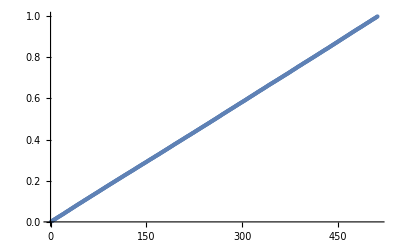

```mathematica
ListPlot[DphiQ2]
```

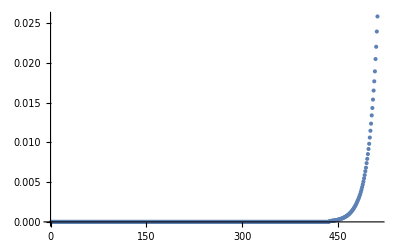

```mathematica
ListPlot[MQ2]
```

```mathematica
Length[MQ2]
```

512

```mathematica
MQ2[[512]]
```

0.0258375

```mathematica
M2[[512]]-Dphi2[[512]]
```

-0.126662

### Time weighted martingale: Traj and quad variation. N = 256, k =3. Run for N * N steps, record last N steps for traj, record values every N steps for quad var. Data:

```mathematica
M3 = {0.135521,0.139844,0.1414,0.140417,0.142158,0.145738,0.145464,0.144812,0.14996,0.146629,0.147234,0.14746,0.14797,0.153013,0.151753,0.153074,0.151262,0.154169,0.153607,0.148197,0.146634,0.148344,0.149748,0.147648,0.146148,0.145652,0.146269,0.14639,0.150294,0.153569,0.149704,0.147943,0.147564,0.144708,0.13697,0.130152,0.131378,0.12534,0.125865,0.131015,0.129569,0.123362,0.123369,0.123321,0.124544,0.128344,0.129996,0.12916,0.127311,0.12943,0.131122,0.124257,0.122758,0.12639,0.126437,0.130311,0.128901,0.129506,0.126088,0.126246,0.129456,0.128676,0.13334,0.126994,0.125178,0.124513,0.124736,0.125371,0.124911,0.130025,0.125828,0.121527,0.119354,0.121109,0.123442,0.119815,0.126392,0.132532,0.128715,0.126186,0.125779,0.125956,0.12671,0.121061,0.124381,0.12519,0.117865,0.11817,0.114689,0.114607,0.113515,0.109276,0.116724,0.115209,0.118624,0.118649,0.120577,0.12268,0.119613,0.115673,0.113463,0.110405,0.109018,0.110884,0.117624,0.118145,0.120357,0.118399,0.124457,0.117528,0.122914,0.126455,0.124075,0.126289,0.132969,0.133207,0.13169,0.131348,0.131302,0.136411,0.131709,0.130579,0.132868,0.135164,0.131151,0.134377,0.134018,0.129318,0.130129,0.129116,0.127989,0.125555,0.127012,0.126933,0.126136,0.125437,0.120572,0.123053,0.119656,0.125184,0.11945,0.114673,0.111324,0.11084,0.114291,0.119942,0.118297,0.120307,0.119076,0.118351,0.118072,0.113516,0.110514,0.112781,0.115836,0.118015,0.124687,0.128676,0.1359,0.130687,0.125495,0.124389,0.129239,0.132222,0.129619,0.128728,0.12538,0.129147,0.129556,0.12531,0.12231,0.117398,0.123308,0.119373,0.119625,0.115511,0.10932,0.109981,0.113775,0.118556,0.114262,0.112888,0.111352,0.110416,0.112001,0.115262,0.121427,0.12135,0.117675,0.112787,0.115933,0.117045,0.116407,0.111682,0.115154,0.112419,0.114283,0.114212,0.106922,0.105559,0.098294,0.100698,0.0964004,0.0971612,0.0960289,0.0965244,0.104078,0.10293,0.100636,0.105115,0.10515,0.104547,0.10908,0.108104,0.105214,0.107256,0.106328,0.103086,0.102022,0.101811,0.105968,0.110168,0.107344,0.105328,0.110278,0.105953,0.106458,0.102081,0.10028,0.095248,0.0940947,0.0917128,0.0945511,0.0963056,0.102631,0.110088,0.106954,0.103654,0.108024,0.108023,0.11212,0.111826,0.117558,0.121878,0.114235,0.114105,0.110003,0.105442,0.103752,0.0979205,0.0956169,0.0956169,0.0963449,0.0936199,0.0987421,0.0933502};
MQ3 = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000110568,0.000127392,0.000148717,0.000174369,0.00020017,0.000230347,0.00026907,0.000309576,0.00035556,0.000409974,0.000473453,0.000550976,0.000642058,0.000746805,0.000865101,0.00099216,0.00113892,0.00131322,0.0015203,0.00177773,0.00203831,0.00238412,0.00276062,0.00319209,0.00370734,0.00433814,0.00495413,0.00571228,0.00672748,0.00784572,0.00919788,0.0106872,0.0124318,0.0144102,0.0165327,0.0191971,0.0220482,0.0251384};
```

```mathematica
Dphi3 = {0.186435,0.191329,0.19273,0.191322,0.19347,0.197331,0.197044,0.19629,0.202326,0.199031,0.199924,0.200693,0.201262,0.207083,0.205732,0.207373,0.205699,0.209043,0.208482,0.202515,0.201093,0.203063,0.204766,0.202462,0.20081,0.201068,0.201538,0.201427,0.205992,0.209136,0.205263,0.203385,0.202922,0.200093,0.19305,0.185523,0.186929,0.180955,0.181309,0.18696,0.185268,0.177908,0.17764,0.177545,0.179159,0.183078,0.184708,0.183752,0.181776,0.183637,0.185569,0.178029,0.176723,0.180867,0.181444,0.185548,0.183818,0.18471,0.181389,0.181304,0.184799,0.183752,0.18906,0.181566,0.179921,0.179298,0.179652,0.180403,0.179701,0.185241,0.180772,0.176558,0.174523,0.176394,0.178852,0.175018,0.182745,0.190234,0.186502,0.183637,0.183084,0.183171,0.184025,0.177829,0.181378,0.182556,0.175641,0.175688,0.171532,0.171432,0.170724,0.166004,0.173531,0.171956,0.175793,0.176008,0.178181,0.18049,0.17705,0.172274,0.169964,0.166259,0.164995,0.166945,0.174524,0.174795,0.17694,0.174865,0.181904,0.174676,0.180556,0.183946,0.181276,0.183144,0.190374,0.190782,0.189345,0.189448,0.1894,0.19512,0.189706,0.188344,0.191166,0.19374,0.189254,0.192844,0.191996,0.186735,0.187595,0.18627,0.185033,0.182318,0.183921,0.183845,0.183394,0.182881,0.177708,0.180719,0.176784,0.183016,0.175921,0.171216,0.167755,0.167255,0.171248,0.1769,0.174951,0.177025,0.176241,0.175712,0.175424,0.170491,0.167398,0.169494,0.173066,0.175141,0.181521,0.18532,0.193027,0.187148,0.182059,0.180829,0.185948,0.188795,0.186129,0.184961,0.181276,0.185322,0.185445,0.180572,0.177269,0.17213,0.178457,0.174119,0.174398,0.169911,0.163092,0.163423,0.167281,0.173019,0.16807,0.167017,0.165328,0.164442,0.166024,0.169261,0.175929,0.175844,0.172017,0.166318,0.169799,0.171182,0.170595,0.166021,0.169499,0.166645,0.168856,0.168779,0.161527,0.159936,0.152553,0.155383,0.150326,0.150605,0.149214,0.149755,0.157393,0.156525,0.153771,0.158364,0.158013,0.157647,0.162864,0.161726,0.158578,0.160802,0.159715,0.15655,0.155432,0.154967,0.159309,0.163782,0.160713,0.158523,0.163694,0.15933,0.15939,0.154276,0.152754,0.147584,0.146376,0.143999,0.146857,0.148758,0.155351,0.162809,0.159657,0.156039,0.160432,0.161147,0.164803,0.164008,0.170676,0.175069,0.167915,0.167181,0.162637,0.158309,0.156486,0.150939,0.148455,0.148455,0.149239,0.146512,0.151719,0.146411};
DphiQ3 = {0.00445283,0.008399,0.0119791,0.0157301,0.019553,0.023603,0.0271597,0.030928,0.0344099,0.0379279,0.0412805,0.0448054,0.0489113,0.0530189,0.0569241,0.0603085,0.0640939,0.0678214,0.0717027,0.075491,0.0794415,0.0834644,0.0878663,0.0918431,0.0954364,0.0993785,0.103206,0.107024,0.110862,0.114719,0.118831,0.122442,0.126272,0.130444,0.134555,0.138964,0.143158,0.146644,0.150345,0.15426,0.157819,0.161479,0.165503,0.16917,0.173506,0.177538,0.18145,0.185299,0.188866,0.192473,0.196959,0.200754,0.204876,0.208861,0.21289,0.217048,0.220857,0.225069,0.229289,0.232759,0.236543,0.240719,0.244869,0.248949,0.253215,0.257168,0.261075,0.265175,0.269072,0.273153,0.276603,0.280477,0.28426,0.28833,0.291957,0.296168,0.300186,0.304034,0.308008,0.311798,0.31527,0.319471,0.323571,0.326996,0.33088,0.334653,0.339043,0.342781,0.346415,0.350557,0.354517,0.358445,0.362671,0.367015,0.371383,0.375398,0.378932,0.382718,0.386728,0.390338,0.394404,0.397816,0.401907,0.405916,0.410032,0.413746,0.417666,0.421031,0.42454,0.428552,0.432543,0.436402,0.440157,0.444067,0.448057,0.452135,0.456141,0.460501,0.464506,0.468828,0.472046,0.475504,0.4797,0.483784,0.487601,0.491389,0.495143,0.498753,0.502679,0.506789,0.510494,0.514826,0.518941,0.522522,0.526692,0.530705,0.534791,0.538787,0.542779,0.547082,0.550508,0.554905,0.558709,0.563064,0.56713,0.571151,0.575101,0.579035,0.582848,0.587053,0.590849,0.595273,0.599306,0.603128,0.606636,0.610516,0.614951,0.619105,0.623069,0.626818,0.631011,0.635408,0.639253,0.643146,0.646994,0.650788,0.654527,0.658573,0.662307,0.666537,0.670501,0.674424,0.678693,0.682483,0.686526,0.690584,0.694521,0.698563,0.702037,0.706041,0.709833,0.713629,0.717717,0.721802,0.725552,0.729441,0.733523,0.737844,0.741882,0.745614,0.749737,0.753914,0.758048,0.761928,0.765789,0.769634,0.773689,0.777224,0.78109,0.784592,0.788607,0.792283,0.795999,0.799955,0.803691,0.807586,0.812042,0.816035,0.819629,0.823515,0.82779,0.832121,0.836273,0.84014,0.844363,0.848186,0.852087,0.855831,0.860161,0.863981,0.868243,0.872671,0.876457,0.880346,0.884583,0.888397,0.892179,0.895942,0.899755,0.903795,0.907951,0.912106,0.916157,0.919904,0.923683,0.927516,0.931427,0.935647,0.939284,0.94346,0.947358,0.951269,0.955304,0.959414,0.96299,0.96675,0.970955,0.975032,0.979297,0.983328,0.987416,0.991473,0.995273,0.999322,1.00306,1.00659};
```

### Analysis

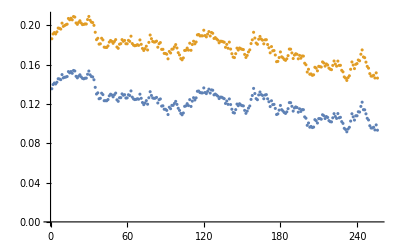

```mathematica
ListPlot[{M3, Dphi3}]
```

### Time weighted martingale: Traj and quad variation. N = 256, k =3. Run for 2 * N * N steps, record last N steps for traj, record values every N steps for quad var. Data:

```mathematica
M4 = {-0.037961,-0.0353638,-0.0334647,-0.0297846,-0.0300801,-0.0310156,-0.0306483,-0.0290143,-0.0258822,-0.0262529,-0.0280035,-0.0282736,-0.0285089,-0.0247246,-0.0254517,-0.0252728,-0.0262222,-0.0273084,-0.0259414,-0.0232757,-0.0228394,-0.0206039,-0.0211413,-0.0231858,-0.025784,-0.0256908,-0.0253937,-0.0268413,-0.0295301,-0.0319571,-0.0337464,-0.0315093,-0.0328185,-0.0316701,-0.0306599,-0.0314449,-0.0319085,-0.0326618,-0.0348465,-0.0315431,-0.0346558,-0.0335127,-0.0364303,-0.0342287,-0.0374452,-0.0362002,-0.0348941,-0.0356503,-0.035551,-0.0385959,-0.0396768,-0.0392617,-0.0365391,-0.0369593,-0.0340695,-0.0354998,-0.0372661,-0.0370554,-0.035964,-0.0375346,-0.0362512,-0.0353703,-0.0336999,-0.0340448,-0.0325615,-0.0330633,-0.0367747,-0.0353134,-0.0352976,-0.037295,-0.0363662,-0.033704,-0.0361866,-0.0362475,-0.0355768,-0.0333687,-0.033218,-0.0324462,-0.0303934,-0.0316436,-0.0298265,-0.0318261,-0.0294587,-0.0277584,-0.0302844,-0.033518,-0.0337531,-0.0324812,-0.0337476,-0.0333169,-0.0333209,-0.0354888,-0.0357632,-0.0387354,-0.0416509,-0.0437318,-0.0448592,-0.0445714,-0.0419916,-0.041282,-0.041282,-0.0435296,-0.044626,-0.0442944,-0.043459,-0.0440227,-0.046434,-0.0425789,-0.0426486,-0.0433207,-0.0454604,-0.0472549,-0.0458212,-0.0452649,-0.0458192,-0.0452473,-0.0430242,-0.0414473,-0.0414696,-0.0413366,-0.037959,-0.0388523,-0.0407008,-0.0430205,-0.0407131,-0.0407954,-0.0374996,-0.0369137,-0.039613,-0.03678,-0.0338121,-0.0319932,-0.0326289,-0.032189,-0.0328245,-0.0327013,-0.0303332,-0.0332213,-0.0324814,-0.0319153,-0.0336681,-0.0321341,-0.0304436,-0.032025,-0.0287786,-0.0292559,-0.028157,-0.026884,-0.0249603,-0.0248278,-0.0227783,-0.0258746,-0.0280107,-0.0281497,-0.0300506,-0.0283206,-0.0261937,-0.0227197,-0.0216066,-0.0205489,-0.0197673,-0.0233835,-0.0236297,-0.0239281,-0.0263236,-0.0284001,-0.0276953,-0.0278614,-0.0291976,-0.0302148,-0.0271565,-0.029257,-0.0318934,-0.0294591,-0.0315679,-0.0347075,-0.034909,-0.0356685,-0.0344157,-0.0319417,-0.030965,-0.0344936,-0.0352057,-0.0355161,-0.0376207,-0.0399144,-0.0399001,-0.0389504,-0.0388551,-0.0396787,-0.0422489,-0.0417005,-0.0449121,-0.046838,-0.0487233,-0.0478132,-0.0508406,-0.0494629,-0.0460334,-0.0476361,-0.0448758,-0.0470918,-0.0450691,-0.045025,-0.0426024,-0.0462143,-0.048117,-0.0482744,-0.04739,-0.0480713,-0.0500345,-0.0523727,-0.0520871,-0.0516082,-0.054964,-0.0541385,-0.051935,-0.0522643,-0.050834,-0.0490281,-0.0458564,-0.0470654,-0.0444291,-0.0428548,-0.0426131,-0.0396471,-0.0393293,-0.0403152,-0.0436079,-0.0432187,-0.0443651,-0.0411747,-0.041446,-0.043138,-0.0417926,-0.0430885,-0.0418656,-0.0426048,-0.0429769,-0.0410789,-0.0419033,-0.0384969,-0.0421215,-0.0428366,-0.0462928,-0.0469763,-0.0455704,-0.048233,-0.0489269,-0.0499041,-0.0500606,-0.0465364,-0.0444749,-0.0480036,-0.0469936,-0.0469161};
```

```mathematica
Dphi4 = {-0.0519522,-0.04923,-0.0472279,-0.0434129,-0.0436858,-0.0445859,-0.044212,-0.0424664,-0.0392088,-0.0394537,-0.0413371,-0.041642,-0.0418082,-0.0379573,-0.038785,-0.0386688,-0.0395998,-0.0407463,-0.0393503,-0.0366564,-0.0361164,-0.0338429,-0.0343894,-0.0363933,-0.0391343,-0.0389823,-0.0386572,-0.0401151,-0.0428785,-0.0453684,-0.0472553,-0.0449696,-0.0463642,-0.0451973,-0.0441994,-0.0450499,-0.045551,-0.0461677,-0.0483868,-0.0450315,-0.0483649,-0.0472586,-0.050378,-0.0481424,-0.0515308,-0.050289,-0.0489842,-0.0497859,-0.049685,-0.0528296,-0.0540106,-0.0535734,-0.0508851,-0.0513274,-0.0482337,-0.0497065,-0.051576,-0.051426,-0.0505047,-0.0521512,-0.0508556,-0.0499293,-0.048172,-0.048509,-0.0470466,-0.0475514,-0.0513836,-0.049894,-0.0498171,-0.0520363,-0.051172,-0.0485109,-0.0511208,-0.0511804,-0.0505378,-0.0481477,-0.0480566,-0.0471782,-0.045021,-0.0462414,-0.0443807,-0.0464002,-0.0439697,-0.0422014,-0.0449166,-0.0482574,-0.048423,-0.0472351,-0.048565,-0.0481842,-0.048381,-0.0505016,-0.0507793,-0.0538319,-0.056675,-0.058859,-0.0601285,-0.0597838,-0.0570767,-0.0563312,-0.0563312,-0.0585989,-0.0597161,-0.0594031,-0.0585872,-0.0589956,-0.0614552,-0.0576312,-0.0576312,-0.0583359,-0.0604295,-0.0622515,-0.0608216,-0.0601666,-0.0606852,-0.0599535,-0.0577079,-0.0561151,-0.0561376,-0.0560611,-0.0525848,-0.0535535,-0.055389,-0.0579527,-0.0554453,-0.0555254,-0.0523919,-0.0518413,-0.0546677,-0.0518818,-0.0487746,-0.0468705,-0.0475119,-0.0471833,-0.0478093,-0.0476698,-0.0451937,-0.0481714,-0.0473972,-0.046805,-0.0486388,-0.0470667,-0.0454476,-0.0470113,-0.0436696,-0.0441688,-0.0430612,-0.0418499,-0.0399104,-0.0397514,-0.0376088,-0.040678,-0.0428532,-0.0430689,-0.0449422,-0.0431503,-0.0410232,-0.0375406,-0.0363495,-0.0353114,-0.0345921,-0.038298,-0.0384362,-0.0387479,-0.0411363,-0.043156,-0.0423906,-0.0425234,-0.0438681,-0.0449547,-0.0419494,-0.0442127,-0.0469173,-0.0443536,-0.0464862,-0.0496896,-0.0498922,-0.0506847,-0.0493276,-0.0468919,-0.045873,-0.049423,-0.0501623,-0.0504254,-0.052541,-0.0548464,-0.055028,-0.0540378,-0.0539925,-0.0548511,-0.0574066,-0.0568556,-0.060203,-0.0622703,-0.0641911,-0.0634296,-0.0665377,-0.065088,-0.061515,-0.0630566,-0.0602445,-0.0625673,-0.0605368,-0.0605597,-0.0581035,-0.0618586,-0.0637852,-0.0640109,-0.0630902,-0.0637737,-0.0658174,-0.0681794,-0.0679457,-0.0674473,-0.0709443,-0.0700641,-0.0677714,-0.0680794,-0.0665829,-0.0647043,-0.061405,-0.0626625,-0.0599806,-0.0582847,-0.058225,-0.0550704,-0.0547008,-0.0557206,-0.0590199,-0.0586153,-0.0598646,-0.0565634,-0.0567719,-0.0583817,-0.0569642,-0.0582991,-0.0570744,-0.0578146,-0.0581519,-0.0562735,-0.0569982,-0.0535882,-0.0572164,-0.0579518,-0.0614208,-0.0620739,-0.0606143,-0.0632786,-0.0639729,-0.0649974,-0.0651598,-0.0616962,-0.0595569,-0.0630286,-0.0619805,-0.0617647};
```

### Analysis

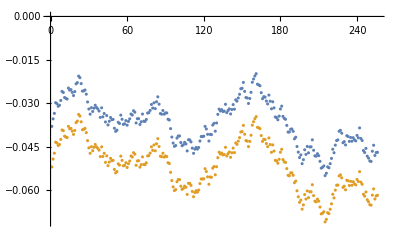

```mathematica
ListPlot[{M4, Dphi4}]
```

### Time weighted martingale: Traj and quad variation. N = 512, k =3. Run for N * N steps, record last N steps for traj. Data:

```mathematica
M5 = {0.104382,0.105263,0.105082,0.105036,0.107949,0.107675,0.10759,0.105756,0.108238,0.110351,0.108715,0.108745,0.111465,0.108637,0.107501,0.109352,0.109352,0.112696,0.110787,0.108199,0.110566,0.109802,0.108728,0.107906,0.110132,0.109373,0.109195,0.10877,0.107815,0.10907,0.106903,0.109425,0.109262,0.109802,0.107943,0.110449,0.109444,0.1076,0.107565,0.10723,0.107693,0.107765,0.111359,0.107667,0.109055,0.107901,0.106898,0.107251,0.105128,0.105625,0.106125,0.109424,0.109179,0.105712,0.108269,0.109989,0.108116,0.10825,0.10825,0.106294,0.1098,0.10922,0.109618,0.106419,0.105678,0.10809,0.108475,0.109545,0.110394,0.109489,0.112465,0.10998,0.109605,0.108426,0.104948,0.101568,0.100944,0.10429,0.102777,0.100085,0.0996676,0.102582,0.104233,0.103428,0.104851,0.10483,0.108162,0.106811,0.105484,0.10399,0.103973,0.105815,0.104323,0.103545,0.101745,0.103321,0.101283,0.0985434,0.0981384,0.0969293,0.0941105,0.0967301,0.0963564,0.0932922,0.09172,0.0930613,0.0929979,0.0949667,0.0978351,0.0988289,0.0990749,0.0975794,0.100135,0.0996676,0.100053,0.100655,0.103021,0.102958,0.103901,0.100051,0.1015,0.103193,0.1056,0.109034,0.108809,0.110753,0.108651,0.108738,0.110795,0.113693,0.114364,0.116808,0.113491,0.113594,0.112974,0.11162,0.109752,0.11314,0.11532,0.112784,0.110974,0.111458,0.109983,0.110213,0.113564,0.116215,0.116288,0.11435,0.112229,0.112797,0.115546,0.113471,0.115785,0.113979,0.116254,0.119036,0.120585,0.120585,0.120225,0.120595,0.120013,0.119167,0.121381,0.123313,0.123259,0.123685,0.125249,0.127863,0.12995,0.130979,0.132567,0.131637,0.129758,0.133123,0.133069,0.135823,0.1371,0.137519,0.137013,0.136506,0.13902,0.136831,0.133226,0.13338,0.132724,0.130569,0.130964,0.129766,0.128306,0.131806,0.131589,0.1309,0.128011,0.131681,0.135309,0.136604,0.138494,0.137792,0.135897,0.13806,0.137874,0.138776,0.136884,0.136531,0.135659,0.133897,0.134545,0.135369,0.138046,0.140345,0.140328,0.139276,0.13581,0.135433,0.134844,0.134865,0.136299,0.137416,0.138938,0.139818,0.136798,0.136719,0.139417,0.138894,0.138947,0.139492,0.139898,0.139765,0.139774,0.140205,0.140242,0.136935,0.139756,0.140128,0.140517,0.143361,0.141009,0.139071,0.139065,0.141129,0.139581,0.140829,0.142853,0.144512,0.148162,0.145209,0.144135,0.144463,0.142379,0.140104,0.136795,0.139927,0.136456,0.137629,0.140402,0.137956,0.137933,0.139662,0.135783,0.135689,0.134965,0.13464,0.130893,0.130019,0.130019,0.12901,0.131946,0.135465,0.138309,0.137769,0.139245,0.139245,0.136248,0.136058,0.136171,0.135138,0.131608,0.129146,0.131195,0.13062,0.128852,0.128386,0.128703,0.1288,0.1288,0.12513,0.128212,0.128799,0.127499,0.126806,0.128469,0.129718,0.129617,0.13321,0.131247,0.130654,0.128686,0.129833,0.131206,0.130977,0.130976,0.130269,0.130851,0.129289,0.128433,0.131637,0.13146,0.132949,0.130409,0.127549,0.127218,0.128937,0.129331,0.129818,0.132082,0.128643,0.129794,0.128687,0.128939,0.130472,0.132257,0.133498,0.134777,0.135103,0.138461,0.13845,0.141018,0.141718,0.141715,0.142762,0.14391,0.143393,0.142743,0.145417,0.145347,0.147906,0.146367,0.144899,0.144958,0.144634,0.1431,0.140254,0.137823,0.140553,0.140151,0.142339,0.143335,0.143344,0.140945,0.143771,0.142047,0.142306,0.142168,0.1409,0.140181,0.138509,0.136047,0.13874,0.141547,0.141012,0.141062,0.138152,0.135621,0.138342,0.138912,0.139879,0.139761,0.140542,0.138776,0.136352,0.134573,0.135439,0.137306,0.13478,0.134784,0.137757,0.133899,0.132761,0.13345,0.133621,0.133285,0.134697,0.132534,0.132719,0.131783,0.128491,0.128751,0.130961,0.133376,0.130773,0.133745,0.130144,0.129739,0.133146,0.130837,0.130676,0.130676,0.1298,0.131242,0.133159,0.132433,0.131939,0.131371,0.134695,0.130967,0.134121,0.137653,0.13776,0.140038,0.136937,0.136027,0.135,0.136334,0.134341,0.13198,0.133338,0.130164,0.131024,0.133864,0.131851,0.130297,0.134127,0.133955,0.131477,0.132204,0.130981,0.131966,0.135628,0.135154,0.135596,0.136333,0.136037,0.133909,0.13621,0.135921,0.135655,0.134958,0.133077,0.131575,0.1323,0.12965,0.129615,0.126749,0.126636,0.128587,0.127985,0.129232,0.129829,0.13261,0.129788,0.129834,0.130222,0.130491,0.130901,0.132415,0.134168,0.132738,0.135847,0.135175,0.136463,0.135978,0.134909,0.131981,0.133446,0.129967,0.127686,0.128927,0.131399,0.13086,0.1345,0.134577,0.131975,0.135724,0.135079,0.135652,0.136296,0.139267,0.138164,0.138171,0.141596,0.141033,0.14025,0.142297,0.14457,0.145675,0.14628,0.147928,0.148622,0.146756,0.14934,0.148925,0.147158,0.145673,0.146085,0.143612,0.14346,0.142093,0.140974,0.141708,0.145756,0.148737,0.149312,0.150029,0.148399,0.147221,0.149769,0.14999,0.148511,0.148935,0.148341,0.146839,0.144365};
```

```mathematica
Dphi5 = {0.0725364,0.0734613,0.0732661,0.0733481,0.0763697,0.0760748,0.0760076,0.0740345,0.0767436,0.0790303,0.0773437,0.0772348,0.079933,0.0769369,0.0757599,0.0776979,0.0776979,0.0810964,0.0791597,0.0763774,0.0789219,0.0783786,0.0774524,0.0766381,0.0789435,0.078128,0.0779369,0.0774968,0.0765015,0.0778491,0.0756519,0.0782905,0.0781866,0.078692,0.0767627,0.0794085,0.078344,0.0763243,0.0763575,0.0761949,0.0766953,0.076824,0.0805414,0.0767229,0.0780906,0.0768949,0.0758801,0.0761799,0.0739026,0.0744847,0.0751047,0.0786429,0.0784347,0.0747264,0.0773953,0.0790968,0.0771021,0.0772458,0.0772458,0.0751844,0.0787338,0.0781339,0.0785451,0.0751083,0.074272,0.0768364,0.0772481,0.0784329,0.0793354,0.0783657,0.0814973,0.0789241,0.0786556,0.0774406,0.0739236,0.070493,0.0698494,0.0734925,0.0718734,0.0691208,0.068746,0.0717435,0.0735008,0.0726396,0.0741272,0.0740383,0.0775452,0.0761698,0.0747701,0.0732301,0.0732827,0.0751826,0.0735637,0.0727877,0.0709152,0.0725289,0.0704135,0.0675562,0.0671233,0.0658311,0.0629275,0.0658319,0.0655026,0.062338,0.0607895,0.0621208,0.0620732,0.064119,0.0669992,0.0680222,0.0682948,0.0667121,0.069441,0.0691029,0.06953,0.0701722,0.072716,0.0726485,0.0736225,0.0697353,0.0712522,0.0731322,0.0755547,0.0791303,0.079044,0.0810445,0.0788633,0.0789521,0.0810021,0.0840511,0.0848938,0.0875102,0.0839845,0.0840944,0.0835554,0.0822219,0.0803721,0.0838649,0.0861048,0.0835592,0.0816449,0.0821144,0.0805853,0.0807584,0.0843282,0.0869771,0.0870518,0.0850626,0.0828299,0.083458,0.0863188,0.084169,0.0866009,0.0846761,0.0870757,0.0899211,0.0915071,0.0915071,0.0910887,0.0914825,0.0909063,0.0900066,0.092263,0.0942463,0.0941213,0.0945744,0.0962376,0.0989506,0.101023,0.102087,0.103715,0.102725,0.1008,0.104304,0.104249,0.107079,0.108395,0.108651,0.10821,0.107691,0.11029,0.107964,0.104133,0.104159,0.10356,0.101433,0.101968,0.100697,0.0992151,0.10286,0.102629,0.101915,0.0989463,0.102772,0.106555,0.107929,0.109994,0.109206,0.107295,0.10959,0.109276,0.110234,0.108152,0.107826,0.106898,0.105045,0.105733,0.106568,0.109406,0.111787,0.111697,0.110581,0.10684,0.106415,0.105856,0.105813,0.107198,0.108327,0.109979,0.110876,0.107722,0.107739,0.110597,0.110076,0.110132,0.11056,0.11095,0.110839,0.110917,0.111374,0.111413,0.107983,0.110921,0.111313,0.11178,0.114794,0.112284,0.110286,0.110204,0.11233,0.110763,0.112035,0.114114,0.115799,0.119448,0.116325,0.115367,0.115566,0.113435,0.1111,0.10767,0.110861,0.107399,0.108518,0.111449,0.108767,0.108813,0.110642,0.106764,0.106665,0.105998,0.105774,0.101889,0.101032,0.101032,0.0999719,0.102961,0.106667,0.109562,0.108991,0.11055,0.11055,0.1075,0.107309,0.107357,0.106344,0.102619,0.100083,0.102167,0.101596,0.0998413,0.0993748,0.0996797,0.0997222,0.0997222,0.0958519,0.0991512,0.0997927,0.0984219,0.0976921,0.0994524,0.100769,0.100662,0.104381,0.102313,0.101711,0.0996446,0.100865,0.102259,0.102088,0.102157,0.10156,0.102203,0.100632,0.0998032,0.103154,0.102968,0.104495,0.101942,0.098979,0.0986495,0.100381,0.100796,0.101357,0.103767,0.100082,0.101265,0.100217,0.100552,0.102147,0.104095,0.105383,0.106638,0.1069,0.11043,0.11042,0.113161,0.113807,0.113672,0.114621,0.115859,0.115263,0.11458,0.11734,0.117373,0.11999,0.118489,0.116947,0.116937,0.116602,0.114933,0.111994,0.10954,0.11226,0.111838,0.114077,0.115056,0.115065,0.1126,0.115584,0.113774,0.113896,0.113709,0.112477,0.111653,0.109892,0.107402,0.110165,0.11311,0.112626,0.112606,0.109484,0.107018,0.109712,0.110334,0.111334,0.111214,0.111976,0.110056,0.10763,0.105768,0.106674,0.108485,0.105883,0.105958,0.108966,0.105073,0.103904,0.104599,0.104765,0.104305,0.105774,0.103486,0.103617,0.102667,0.0993453,0.0995535,0.101796,0.104233,0.101582,0.104459,0.10082,0.10029,0.10361,0.101212,0.101122,0.101122,0.100206,0.101745,0.103784,0.103136,0.102598,0.101975,0.105379,0.101623,0.104801,0.108359,0.108468,0.110848,0.107857,0.10694,0.105932,0.107263,0.105201,0.102783,0.104077,0.100948,0.101799,0.104715,0.102634,0.10107,0.104925,0.104745,0.10217,0.102982,0.101727,0.102783,0.106534,0.105932,0.106266,0.107007,0.10671,0.10469,0.107122,0.106837,0.106559,0.105821,0.103875,0.102443,0.1032,0.100436,0.100335,0.0974553,0.0974076,0.0993741,0.0988281,0.100062,0.100662,0.103336,0.10044,0.10044,0.100932,0.101165,0.101608,0.103245,0.10499,0.103553,0.106645,0.106088,0.107327,0.106878,0.105765,0.102756,0.104281,0.100834,0.0985279,0.0998201,0.102394,0.10178,0.105431,0.105436,0.102798,0.106698,0.106009,0.106658,0.10728,0.11032,0.109215,0.109192,0.112607,0.112043,0.111171,0.1133,0.115597,0.116803,0.117379,0.119092,0.119796,0.117928,0.120561,0.120145,0.118286,0.11697,0.117394,0.114973,0.114815,0.113558,0.112461,0.113165,0.117069,0.120132,0.120616,0.121334,0.119703,0.118568,0.121188,0.121363,0.119873,0.120254,0.1196,0.118097,0.115576};
```

### Analysis

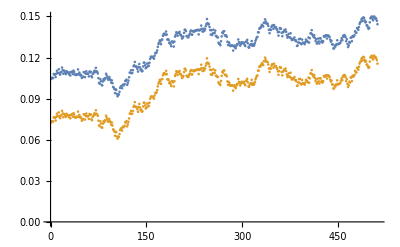

```mathematica
ListPlot[{M5, Dphi5}]
```